## Exercise 1

We are interested in estimating an unknown signal  , given noisy measurements . The signal is drawn from a prior distribution , and the noisy observation process is characterized by the conditional distribution   called Likelihood. This defines the framework of Bayesian estimation.
Indeed using Bayes’ theorem, the posterior distribution of   given , is:
													

In the exercise I will consider the case of having gaussian noise with variance  and mean 0, so that if  is the true value, we will  have  observations:
													       with      
													 
We want to study the performance of the Maximum A Posteriori (MAP) estimator:        , in terms of the Mean Square Error (MSE), for which the Bayes-optimal estimator is: .
 The notion of Bayes-optimal estimator of a particular error, refer to the estimator that given the posterior ,  gives an estimation of , that on average minimize the error under examination.
 In this exercise, we will consider three different priors, associated to:
 1. A Rademacher random variable, , with probability p=0.5
 2. A 	Gaussian random Variable  
 3. A Gauss-Bernoulli  random variable which is 0 with probability 1/2 and Gaussian otherwise. It basically represent the fact that half of the times the signal is missing.
 
 The posteriors for this model can be computed from the priors, the fact that the likelihood is Gaussian, and imposing the normalization. The probabilities implemented in the code are indeed  the expression obtained for them in the textbook.

```mathematica
(*Define the sampling for the different RVs*)
xRad = Sign[Random[] - 0.5]; 
xGauss = Sqrt[2]*InverseErf[2*Random[]-1];
xGaussBernoulli = If[Random[] < 0.5, 0, Sqrt[2]*InverseErf[2*Random[] - 1]];
```

```mathematica
(* In general the goal will be to generate  noisy observations with mean 0 and variance Delta, and then try to recover them back *)
Delta = 3;
n = 1000;

yRad = Table[
   xRad + Sqrt[2*Delta]*InverseErf[2*Random[] - 1],
  {i, 1, n}
];
yGauss = Table[
    xGauss + Sqrt[2*Delta]*InverseErf[2*Random[] - 1],
  {i, 1, n}
];

yGaussBernoulli = Table[
  xGaussBernoulli + Sqrt[2*Delta]*InverseErf[2*Random[] - 1],
  {i, 1, n}
];


(* Length of the table (Number of observations) *)
Length[yRad]
```

1000

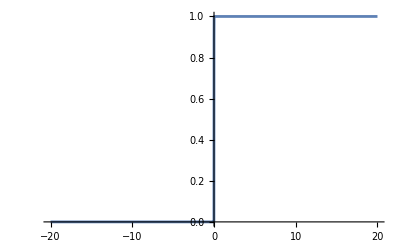

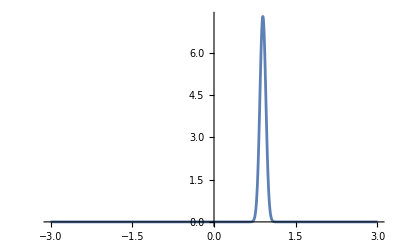

General::munfl: 1. 5.72934496226×10^-940 is too small to represent as a normalized machine number; precision may be lost.

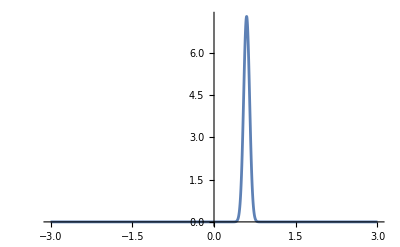

```mathematica
(*Now we have our noisy data, we want to find back the true value, giving the best estimation*)
(*Thruogh the Bayes theorem is possible to find the exact form of the posterior probability 
P(x|Y)for the three models*)
Prad[x_,yRad_,Delta_]:=1/(1+Exp[-2*x*Total[yRad]/Delta]);
Pgauss[x_,yGauss_,Delta_,n_]:=PDF[NormalDistribution[Total[yGauss]/(n+Delta),Sqrt[Delta/(n+Delta)]],x];
PgaussBernoulli[x_,yGaussBernoulli_,Delta_,n_]:=Module[{mean,variance,z,weight1,weight2,gaussian},mean=Total[yGaussBernoulli]/(n+Delta);
variance=Delta/(n+Delta);
z=mean^2/(2*variance);
weight1=1/(1+(Delta/(n+Delta)) Exp[-z]);
weight2=1/(1+((n+Delta)/Delta) Exp[-z]);
gaussian=PDF[NormalDistribution[mean,Sqrt[variance]],x];
weight1 DiracDelta[x]+weight2 gaussian];

(*Plot the posterior distributions*)
Plot[Prad[x,yRad,Delta],{x,-20,+20}]
Plot[Pgauss[x,yGauss,Delta,n],{x,-3,+3},PlotRange->All]
Plot[PgaussBernoulli[x,yGaussBernoulli,Delta,n],{x,-3,+3},PlotRange->All]
```

General::munfl: Exp[-2160.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1938.57] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

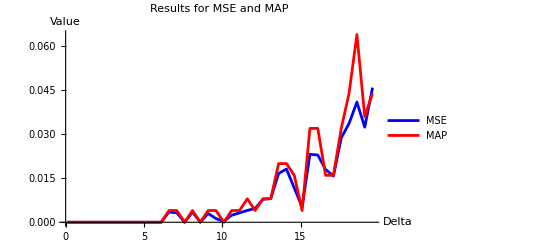

```mathematica
(*Consider the evolution of the error, avaraged over many observations, either with the sample size n, or the noise variance Delta, for MAP and MMSE estimator*)
(*Rademcher *)
Prad[x_,yRad_,Delta_]:=1/(1+Exp[-2*x*Total[yRad]/Delta]);
ResultsRadMSE ={};
ResultsRadMAP = {};
Delta = 1;
n=100;
(*UNCOMMENT JUST ONE OF THE TWO FOR TO ITERATE OVER DELTA OR n*)
For[Delta = 0.1,Delta <= 20,Delta=Delta+0.5,
(*For[n = 100,n <= 10000,n=10*n,*)
MSE=0;
MAPMSE = 0;
For[instances = 0,instances <1000, instances++,
	(*Generate different instance at each iteration*)
	    xRad = Sign[Random[] - 0.5];
	    yRad = Table[xRad + Sqrt[2*Delta]*InverseErf[2*Random[] - 1],  {i, 1, n}];
		xRadMAP=If[Prad[1,yRad,Delta]>Prad[-1,yRad,Delta], 1, -1];
		xRadMMSE=Prad[1,yRad,Delta]-Prad[-1,yRad,Delta];
	    MSE = MSE + (xRadMMSE-xRad)^2; (*Sum to take the avg at the end*)
	   MAPMSE = MAPMSE +(xRadMAP-xRad)^2;
];
(*take the avarage of the mean square error among all the observations*)
	AppendTo[ResultsRadMSE,{Delta,MSE/(1000)}] ;
	AppendTo[ResultsRadMAP,{Delta,MAPMSE/(1000)}] ;
];

ListPlot[{ResultsRadMSE,ResultsRadMAP},PlotStyle->{Blue,Red},PlotLegends->{"MSE","MAP"},AxesLabel->{"Delta","Value"},PlotLabel->"Results for MSE and MAP",Joined->True ,PlotRange->All]
```

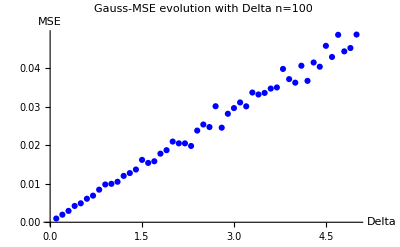

plotImage.png

```mathematica
ResultsGauss ={};
Pgauss[x_,yGauss_,Delta_,n_]:=PDF[NormalDistribution[Total[yGauss]/(n+Delta),Sqrt[Delta/(n+Delta)]],x];
For[Delta = 0.1,Delta <= 5,Delta = Delta + 0.1,
(*For[n = 100,n <= 10000,n=10*n,*)
n=100;
MSE=0; (*Map and MMSE coincide for a Gaussian*)
For[instances = 0,instances <600, instances++,
	    xGauss = Sqrt[2]*InverseErf[2*Random[]-1];
	    yGauss = Table[xGauss + Sqrt[2*Delta]*InverseErf[2*Random[] - 1],{i, 1, n}];
		  xGaussMAP = ArgMax[Pgauss[x,yGauss,Delta,n],x];
	   xGaussMMSE = NIntegrate[Pgauss[x,yGauss,Delta,n]*x,{x,-Infinity,+Infinity}];
	    MSE = MSE + (xGaussMMSE-xGauss)^2; (*Sum to take the avg at the end*)
];
	AppendTo[ResultsGauss,{Delta,MSE/(600)}] ;
(*take the avarage of the mean square error among all the observations*)
];
ResultsGauss;
plot = ListPlot[ResultsGauss,PlotStyle->Blue,AxesLabel->{"Delta","MSE"},PlotLabel->"Gauss-MSE evolution with Delta n=100"]
Export["plotImage.png",plot]
```

General::munfl: Exp[-919.264] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

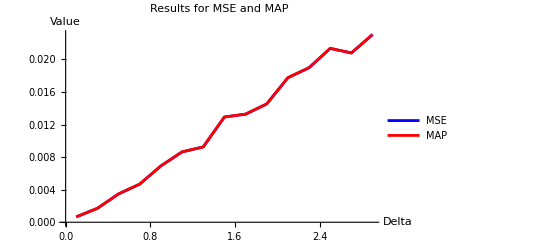

```mathematica
PgaussBernoulli[x_,yGaussBernoulli_,Delta_,n_]:=Module[{mean,variance,z,weight1,weight2,gaussian},mean=Total[yGaussBernoulli]/(n+Delta);
variance=Delta/(n+Delta);
z=mean^2/(2*variance);
weight1=1/(1+(Delta/(n+Delta)) Exp[-z]);
weight2=1/(1+((n+Delta)/Delta) Exp[-z]);
gaussian=PDF[NormalDistribution[mean,Sqrt[variance]],x];
weight1 DiracDelta[x]+weight2 gaussian]

ResultsGaussBernoulliMMSE ={};
ResultsGaussBernoulliMAP ={};
For[Delta = 0.1,Delta <= 3,Delta = Delta + 0.2,

n=100;
MSE=0;
MAPMSE = 0;
For[instances = 0,instances <1000, instances++,
	    xGaussBernoulli = If[Random[] < 0.5, 0, Sqrt[2]*InverseErf[2*Random[] - 1]];
	    yGaussBernoulli = Table[xGaussBernoulli + Sqrt[2*Delta]*InverseErf[2*Random[] - 1],{i, 1, n}];
		  xGaussBernoulliMAP = ArgMax[PgaussBernoulli[x,yGaussBernoulli,Delta,n],x];
	   xGaussBernoulliMMSE = NIntegrate[PgaussBernoulli[x,yGaussBernoulli,Delta,n]*x,{x,-Infinity,+Infinity}];
	    MSE = MSE + (xGaussBernoulliMMSE-xGaussBernoulli)^2; (*Sum to take the avg at the end*)
	    MAPMSE = MAPMSE + (xGaussBernoulliMAP-xGaussBernoulli)^2;
];
	(*take the avarage of the mean square error among all the observations*)
	AppendTo[ResultsGaussBernoulliMMSE,{Delta,MSE/(1000)}] ;
	AppendTo[ResultsGaussBernoulliMAP,{Delta,MSE/(1000)}] ;
	
];
ResultsGauss;
ListPlot[{ResultsGaussBernoulliMMSE,ResultsGaussBernoulliMAP},PlotStyle->{Blue,Red},PlotLegends->{"MSE","MAP"},AxesLabel->{"Delta","Value"},PlotLabel->"Results for MSE and MAP",Joined->True ]
```